```mathematica
alphaH[V_]:=0.07*E^(-V/20);
betaH[V_]=1/(E^((30-V)/10)+1);
h0[V_]=alphaH[V]/(alphaH[V]+betaH[V]);

alphaM[V_]=((0.1*(25-V))/(E^((25−V)/10)−1));
betaM[V_]=(4*E^(-V/18));
m0[V_]=alphaM[V]/(alphaM[V]+betaM[V]);

alphaN[V_]=(0.01*(10-V))/(E^((10-V)/10)-1);
betaN[V_]=0.125*E^(-V/80);
n0[V_]=alphaN[V]/(alphaN[V]+betaN[V]);

τm[V_]=1/(alphaM[V]+betaM[V]);
τn[V_]=1/(alphaN[V]+betaN[V]);
τh[V_]=1/(alphaH[V]+betaH[V]);

GK=34;
VK=-11;
JK[V_]=GK*n0[V]^4*(V-VK);

GNa=120;
VNa=109;
JNa[V_]=GNa*m0[V]*h0[V]*(V-VNa);

GL = 0.26;
VL = 11;

a=238*10^(-3);
c = 1.5*10^(-4);          (*Membrance Capacitance*)
r = 2*10^4;                      (*Membrane Resistance*)
curent=50;
```

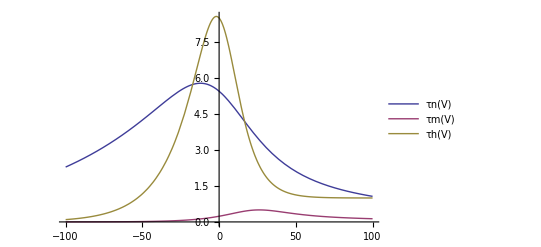

```mathematica
Plot[{τn[V],τm[V],τh[V]},{V,-100,100},PlotRange->All,PlotLegends->"Expressions"]
```

{{m[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

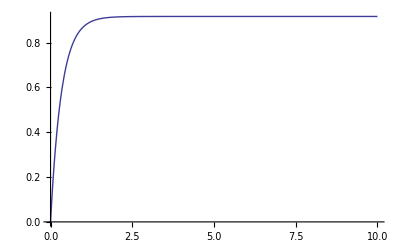

```mathematica
difm=NDSolve[{m'[t]==-(m[t]-m0[curent])/(τm[curent]),m[0]==0},m[t],{t,0,10}]
Plot[Evaluate[m[t]/.difm],{t,0,10},PlotRange->All]
```

{{H[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

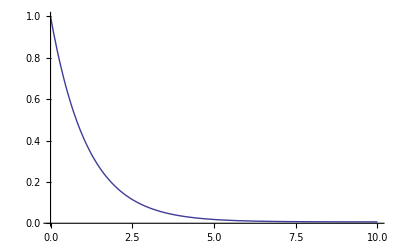

```mathematica
difh=NDSolve[{H'[t]==-(H[t]-h0[curent])/(τh[curent]),H[0]==1},H[t],{t,0,10}]
Plot[Evaluate[H[t]/.difh],{t,0,10},PlotRange->All]
```

{{n[t]→InterpolatingFunction[{{0.,10.}},<>][t]}}

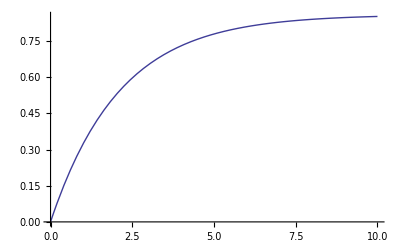

```mathematica
difn=NDSolve[{n'[t]==-(n[t]-n0[curent])/(τn[curent]),n[0]==0},n[t],{t,0,10}]
Plot[Evaluate[n[t]/.difn],{t,0,10},PlotRange->All]
```

```mathematica
β=0.4;
α=(β^2)/(3*r*c);

T=10;
X=15;
length=Ceiling[X/β];
hight=Ceiling[T/α];
ϕ0[x_]= If[x<2,50,0];

m00 = m0[0];
h00=h0[0];
n00=n0[0];

valuesV = Table[0,{i,hight},{j,length}];
valuesM = Table[m00,{i,hight},{j,length}];
valuesH = Table[h00,{i,hight},{j,length}];
valuesN = Table[n00,{i,hight},{j,length}];

For[i = 1, i<length,i++, valuesV[[1,i]] = ϕ0[(i-1)*β]];
Clear[i];
α
```

0.0177778

```mathematica
For[j=2,j<=hight,j++,
	For[i = 1, i <= length, i++,
        valuesM[[j,i]]= valuesM[[j-1,i]] - α*((valuesM[[j-1,i ]]- m0[valuesV[[j-1,i]]])/τm[valuesV[[j-1,i]]]);
        valuesH[[j,i]]= valuesH[[j-1,i]] - α*((valuesH[[j-1,i ]]- h0[valuesV[[j-1,i]]])/τh[valuesV[[j-1,i]]]);
        valuesN[[j,i]]= valuesN[[j-1,i]] - α*((valuesN[[j-1,i ]]- n0[valuesV[[j-1,i]]])/τn[valuesV[[j-1,i]]]);
  If[i≠ 1&&i≠ length,valuesV[[j,i]]=-2* Pi *a*( GNa*(valuesV[[j-1,i]]-VNa)*(valuesM[[j-1,i]]^3)*valuesH[[j-1,i]]*α+GK*(valuesV[[j-1,i]]-VK)*(valuesN[[j-1,i]]^4)*α +GL*(valuesV[[j-1,i]]-VL)*α - ((1/(r*c))*((valuesV[[j-1,i+1]]-2*valuesV[[j-1,i]]+valuesV[[j-1,i-1]])/β^2))*α )+ valuesV[[j-1,i]];];]]
Clear[i,j];
```

```mathematica
impulse =  Animate[ListPlot[Table[{(i-1)*β,valuesV[[j,i]]},{i,1,length,1}], PlotRange->All],{j,1,hight,1}]
```

```mathematica
Export["C:\\Users\\Niki\\Desktop\\impulse50.avi", impulse]
```

C:\Users\Niki\Desktop\impulse50.avi